```mathematica
AppendTo[$Path,"/Users/Daan/Documents/GitHub/self-organising-regulation/mathematica_notebooks_minimal_GRDS_model/"];
<<plottingfunctions`
pars={ϕ->0.5,f->0.1,T->10};
SetOptions[{Plot, ListLinePlot, ListPlot,Plot3D,DensityPlot,LogLogPlot,LogLinearPlot,LogPlot}, {PlotTheme->{"Scientific","SansLabels","VibrantColor"}}];
SetOptions[{Plot, ListLinePlot, ListPlot, ContourPlot,DensityPlot,LogLogPlot,LogLinearPlot,LogPlot}, {Frame->True,BaseStyle->{FontSize->20,FontFamily->"Helvetica"}, FrameStyle->Black,LabelStyle->{Black,FontSize->16,FontFamily->"Helvetica"}}];
SetOptions[{Plot3D}, {BaseStyle->{FontSize->16,FontFamily->"Helvetica"}}];
Offpaclet:ref/Off[FindMinimum::reged]
Offpaclet:ref/Off[FindMaximum::reged]
colormaps={"Default"->97,"Earth"->98,"Garnet"->99,"Opal"->100,"Sapphire"->101,"Steel"->102,"Sunrise"->103,"Textbook"->104,"Water"->105,"BoldColor"->106,"CoolColor"->107,"DarkColor"->108,"MarketingColor"->109,"NeonColor"->109,"PastelColor"->110,"RoyalColor"->111,"VibrantColor"->112,"WarmColor"->113};
(*Apple colors*)blue=RGBColor[17.6/100,41.6/100,63.1/100];
green=RGBColor[34.9/100,66.7/100,33.3/100];
yellow=RGBColor[96.9/100,68.6/100,20.8/100];
red=RGBColor[86.3/100,13.3/100,19.6/100];
purple=RGBColor[55.3/100,27.5/100,55.7/100];
grey=RGBColor[55.7/100,57.3/100,56.9/100];
(*4 Apple colors*)
apple4={green,red,grey,purple};
```

RefLink[Off,paclet:ref/Off][The point `1` is at the edge of the search region `3` in coordinate `2` and the computed search direction points outside the region.]

RefLink[Off,paclet:ref/Off][The point `1` is at the edge of the search region `3` in coordinate `2` and the computed search direction points outside the region.]

```mathematica
GLOBALPARS={MAXPHI->1000,PLOTPOINTS->30};
```

## Derivations without GRDS

We solve the system described in Equation [2] of the main text . We simulate the growth of the number of cells in an adapted phenotype n_g and in a non-adapted phenotype, respectively with growth rate μ=1 and one with growth rate μ=0. Cells can switch in between the phenotypes: the switching rate from fast to slow is ϕ, and the switching rate from slow to fast is ϕ/(n-1). In this notebook, we will (for analytical purposes) often use f:=1□ with 0<f<1, and . Initially, the population has a fraction p_0 in the fast phenotype, and the duration of one environment is given by T. We get the analytical solution:

```mathematica
analyticalSol = DSolve[{ng'[t] == (1 -ϕ) ng[t]+f ϕ nb[t],nb'[t]== -f ϕ nb[t]+ϕ ng[t],ng[0]==p0 ,nb[0]==(1-p0) },{ng[t],nb[t]},t];
```

This solution can be simplified somewhat by using information about our parameters in the FullSimplify-command.

```mathematica
analyticalSol2 = FullSimplify[analyticalSol,Assumptions -> {p0>0,p0<1,f>0,f<1,ϕ>0,t≥0}]
```

{{nb[t]→1/(2 √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))ⅇ^(-1/2 t (-1+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))) (1+(-1+f) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))-p0 (1+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))+ⅇ^(t √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))) (-1+p0+(1+f (-1+p0)+p0) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))-p0 √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))),ng[t]→1/(2 √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))ⅇ^(-1/2 t (-1+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))) (2 (-1+ⅇ^(t √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))) f ϕ+p0 (-1+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))+ⅇ^(t √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))) (1-(1+f) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))))}}

We can gather these solutions in a vector n(ϕ,f,p0,t),

```mathematica
n[ϕ_,f_,p0_,t_]:=Evaluate[{ng[t],nb[t]}/.analyticalSol2[[1]]]
```

And the total population size is then given by the dot product with the vector [1,1]:

```mathematica
ntot[ϕ_,f_,p0_,t_]:=Evaluate[FullSimplify[n[ϕ,f,p0,t].{1,1},Assumptions->{ϕ>0,t≥0,p0>0,p0<1,f>0,f<1}]]
ntot[ϕ,f,p0,t]
```

1/(2 √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))ⅇ^(-1/2 t (-1+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))) (1-2 p0-(1+f) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))+ⅇ^(t √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))) (-1+2 p0+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))))

Using these functions, we can calculate the fraction of the population in the good state at time t.

```mathematica
frac[ϕ_,f_,p0_,t_]:=Evaluate[FullSimplify[n[ϕ,f,p0,t][[1]]/ntot[ϕ,f,p0,t],Assumptions -> {f>0,f<1,p0>0,p0<1,ϕ>0,t>=0}]]
frac[ϕ,f,p0,t]
```

(2 (-1+ⅇ^(t √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))) f ϕ+p0 (-1+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))+ⅇ^(t √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))) (1-(1+f) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))))/(1-2 p0-(1+f) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))+ⅇ^(t √(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))) (-1+2 p0+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))))

### Analysis of the fraction of good cells at large T

We can write this a bit more concisely if we relabel the expression under the square root as D:

```mathematica
simplifiedfrac = Simplify[frac[ϕ,f,p0,t],D==1+ϕ (-2+ϕ+f (2+(2+f) ϕ))]
```

(√D (1+ⅇ^(√D t)) p0+2 (-1+ⅇ^(√D t)) f ϕ-(-1+ⅇ^(√D t)) p0 (-1+ϕ+f ϕ))/(√D (1+ⅇ^(√D t))+(-1+ⅇ^(√D t)) (-1+2 p0+ϕ+f ϕ))

It is not entirely obvious from this expression that the large t limit is independent of the initial fraction (p0):

```mathematica
largetlimitnonsimplified = Limit[frac[ϕ,f,p0,t],t->Infinity,Assumptions->{p0<1,p0>0,f<1,f>0,ϕ>0}]
```

(2 f ϕ+p0 (1-(1+f) ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ)))))/(-1+2 p0+ϕ+f ϕ+√(1+ϕ (-2+ϕ+f (2+(2+f) ϕ))))

```mathematica
largetlimit = Limit[simplifiedfrac,t->Infinity,Assumptions->{D>0,p0<1,p0>0,f<1,f>0,ϕ>0}]
```

(2 f ϕ+p0 (1+√D-(1+f) ϕ))/(-1+√D+2 p0+ϕ+f ϕ)

But we can cancel the terms with p0 (manually) to obtain the following large t limit 1/2 (1+√D-f ϕ-ϕ), which is confirmed by Mathematica:

```mathematica
FullSimplify[largetlimitnonsimplified==1/2 (1+√D-f ϕ-ϕ),D==1+ϕ (-2+ϕ+f (2+(2+f) ϕ))]
FullSimplify[largetlimit==1/2 (1+√D-f ϕ-ϕ),D==1+ϕ (-2+ϕ+f (2+(2+f) ϕ))]
```

True

True

### Behaviour after several periods of growth

When the environment duration is constant and the dynamics is always following the system as above, the final fraction of cells in the good phenotype is always given by frac(ϕ,f,p0,T) in terms of the initial fraction. The new initial fraction is then given by p0^new=f(1-frac(ϕ,f,p0^old)). The figure below shows that p0^new will stabilise after a few iterations.

```mathematica
Manipulate[CobwebPlot[f(1-frac[ϕ,f,#,T])/.{ϕ->0.02,f->0.33,T->3}&,p0init,10,{0,1},PlotRange->{{0,1},{0,1}},Frame->True,Axes->False,CobStyle->Directive[Dashed,Red],PlotRangePadding->None],{p0init,0.,1}]
```

We can also solve the fixed point equation

```mathematica
p0sols=Solve[(1-frac[ϕ,f,p0,T])f == p0,p0];
p0sols/.{ϕ->0.5,f-> 0.1,T-> 100000}
Simplify[p0/.p0sols[[1]],D==1+ϕ (-2+ϕ+f (2+(2+f) ϕ))]
```

{{p0→0.04577855615},{p0→-0.09221443851}}

1/(4 (-1+ⅇ^(√D T)))(-1+ⅇ^(√D T)-f+ⅇ^(√D T) f-√D (1+ⅇ^(√D T)) (1+f)+ϕ-ⅇ^(√D T) ϕ-f^2 ϕ+ⅇ^(√D T) f^2 ϕ+√(-4 (-1+ⅇ^(√D T))^2 f+2 D (1+4 ⅇ^(√D T) f+f^2+ⅇ^(2 √D T) (1+f^2))-2 √D (-1+ⅇ^(2 √D T)) (-1+f) (-1+f+ϕ+2 f ϕ+f^2 ϕ)))

It is clear that we want to go with the first solution since it’s the only positive one, so let’s keep that one:

```mathematica
p0sol[ϕ_,f_,T_]:=Evaluate[p0/.p0sols[[1]]]
```

### Expression for the average growth rate

We can then insert this starting fraction in our function for the total number of cells (n_tot), or we can immediately calculate the average growth rate:

```mathematica
G[ϕ_,f_,T_]:=Log[ntot[ϕ,f,p0sol[ϕ,f,T],T]]/T
Gnum[ϕ_?NumericQ,f_?NumericQ,T_?NumericQ]:=Log[ntot[ϕ,f,p0sol[ϕ,f,T],T]]/T
```

### For small enough T and large enough n-1 (small enough f), the optimal switching rate becomes 0

A switching rate of 0 can become optimal for some parameters. Let us investigate when this happens. We can calculate for which the derivative of the average growth rate to ϕ can become negative at ϕ=0.

```mathematica
dntotdphi = FullSimplify[D[ntot[ϕ,f,p0sol[ϕ,f,T],T],ϕ]/.ϕ->0,{f>0,f<1,T>0}]
dGdphi = FullSimplify[D[G[ϕ,f,T],ϕ]/.ϕ->0,{f>0,f<1,T>0}]
```

(f (1-f+√((-1+f)^2+4 ⅇ^T f)) (-2+(-1+f) T)-2 ⅇ^T f (-1+f-√((-1+f)^2+4 ⅇ^T f)+T+f T))/(2 √((-1+f)^2+4 ⅇ^T f))

(T+f^2 T-√((-1+f)^2+4 ⅇ^T f) T+f (-4+4 ⅇ^T-(2+√((-1+f)^2+4 ⅇ^T f)) T))/(2 √((-1+f)^2+4 ⅇ^T f) T)

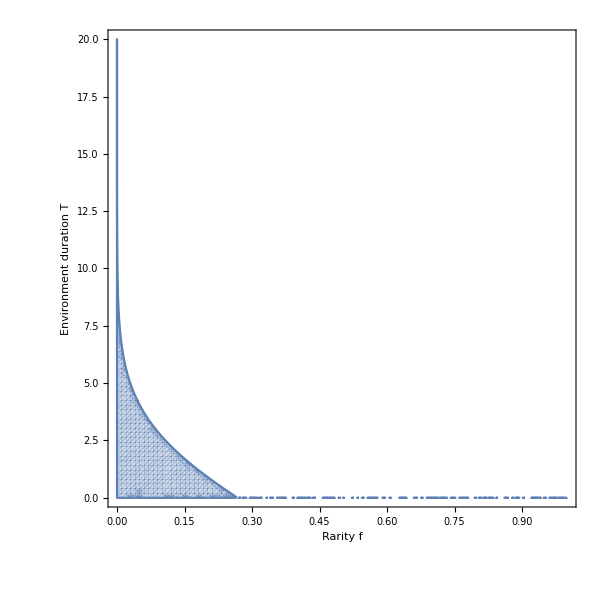

```mathematica
RegionPlot[Evaluate[dntotdphi]<0,{f,0,1},{T,0,20},PlotPoints->100,Frame->True, BaseStyle -> {FontFamily -> "Helvetica",FontSize -> 18},ImageSize->600,FrameLabel->{"Rarity f","Environment duration T"}]
```

So, it is clear that a minimal switching rate is optimal for small f, which is analogous to the situation with many bad phenotypes. We can investigate this a little further. Let’s investigate for which f the derivative dn/dphi becomes positive, i.e., switching becomes favorable. We only take the numerator divided by f, since the denominator is always positive and f=0 is a trivial solution.

```mathematica
numerator[f_,T_]:=(1-f+√((-1+f)^2+4 ⅇ^T f)) (-2+(-1+f) T)-2 ⅇ^T (-1+f-√((-1+f)^2+4 ⅇ^T f)+T+f T)
fcrits[T_]:=f/.Solve[numerator[f,T]==0,f]
```

```mathematica
fcrits[T][[1]]
```

(4-8 ⅇ^T+4 ⅇ^(2 T)+4 T-4 ⅇ^T T+2 T^2-2 ⅇ^T T^2-√(-4 (2 T-2 ⅇ^T T+T^2+ⅇ^T T^2)^2+(-4+8 ⅇ^T-4 ⅇ^(2 T)-4 T+4 ⅇ^T T-2 T^2+2 ⅇ^T T^2)^2))/(2 (2 T-2 ⅇ^T T+T^2+ⅇ^T T^2))

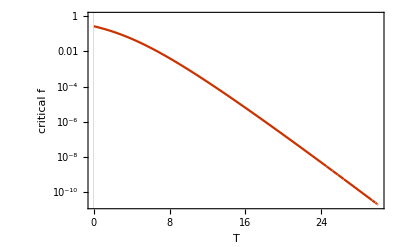

```mathematica
LogPlot[Evaluate[fcrits[T]][[1]],{T,0.0001,30},FrameLabel->{T,"critical f"}]
```

Three conclusions: 1) we should only care about the first solution of the above. 2) For relatively short environment times, there is a minimal rarity (or maximal number of bad phenotypes) for which switching is not favourable at all. This critical rarity goes down (more or less) exponentially. 3) It is clear, however, that switching always becomes favourable when the environment durations are long enough:

```mathematica
fcrit[T_]:=Evaluate[fcrits[T][[1]]]
```

### Optimal switching rates

We can now numerically maximise the average population growth rate, to find the optimal switching rate ϕ

```mathematica
pars3={T->10,f->0.1};
optphi[f_?NumericQ,T_?NumericQ] := If[f>=fcrit[T],ϕ/.Last[FindMaximum[Evaluate[Gnum[ϕ,f,T]],{ϕ,0.1,0,MAXPHI/.GLOBALPARS}]],0]
```

A visual analysis shows that bet-hedging clearly gives a large fitness advantage, and that the optimal switching rates seem to go like 1/T for large enough T.

```mathematica
plotmaxG = Plot[Evaluate@Table[Gnum[optphi[f,T],f,T],{f,{0.001,0.01,0.1,0.5}}],{T,.1,30},PlotLegends->LineLegend[Table[f,{f,{0.001,0.01,0.1,0.5}}],LegendLabel->f],FrameLabel->{"Environment Duration","average growth rate"},ImageSize->400,ImagePadding->{{60,5},{50,10}}];
plotzerophiG=Plot[Evaluate@Table[G[0,f,T],{f,{0.001,0.01,0.1,0.5}}],{T,.1,30},PlotLegends->LineLegend[Table[f,{f,{0.001,0.01,0.1,0.5}}],LegendLabel->"ϕ=0"],PlotStyle->Dashed,FrameLabel->{"Environment Duration","average growth rate"},ImageSize->400,ImagePadding->{{60,5},{50,10}}];
plotargmaxphi = Plot[Evaluate@Table[optphi[f,T],{f,{0.001,0.01,0.1,0.5}}],{T,.1,30},PlotLegends->LineLegend[Table[f,{f,{0.001,0.01,0.1,0.5}}],LegendLabel->f],FrameLabel->{"Environment Duration","Optimal switching rate (ϕ)"},ImageSize->400,ImagePadding->{{70,15},{50,20}}];
```

```mathematica
GraphicsColumn[{Show[plotmaxG,plotzerophiG],plotargmaxphi},ImageSize->800,Spacings->-30]
```

-Graphics-

### Limit for large environment durations

It is clear from the figures above that switching makes an important difference especially when T→Infinity. This may be surprising because the one parameter that differs between the two scenarios (ϕ>0 or ϕ=0) is decreasing such that they become more and more the same, while the results do not move closer. We will investigate this case a bit closer. Mathematica gives the following counterintuitive results: 1) if we insert ϕ=0, and then take the limit for large T the result is 1/2, while 2) if we first take the limit for large T, and then insert ϕ=0, the result is 1:

```mathematica
Limit[G[0,f,T],T->Infinity,Assumptions->{f<1,f>0,ϕ>0}]
longTlimit=Limit[G[ϕ,f,T],T->Infinity,Assumptions->{f<1,f>0,ϕ>0}]
longTlimit/.ϕ->0
```

1/2

1/2 (1-(1+f) ϕ+√(1+2 (-1+f) ϕ+(1+f)^2 ϕ^2))

1

Let us first investigate the first case. If the cells do not switch, then the differential equations are given by:

```mathematica
ngphi0[t_,p0_]:=p0 E^t;
nbphi0[t_,p0_]:=1-p0
```

Thus, in each environment the adapted cells will grow e^T-fold. In the next environment, a fraction f of the non-adapted cells will start growing, i.e. f(1-p_0). In the third environment however, we assume that again a fraction f of the non-adapted cells will start growing, but there are now (1-f)(1-p_0)+p_0 e^T non-adapted cells, i.e. cells that were never adapted, and cells that were adapted to the first environment, but not to the second. If the environment duration is long enough, the first term will be negligible. Therefore, a fraction f of the p_0 E^T cells will start to grow again. This process will repeat itself, so that after 2n environments, there will be 2(p_0 E^T fE^T f... E^T)=2 p_0 f^n E^nT cells. This will give an average growth rate of 1/(2nT)log(2 p_0 f^n E^nT)=(log(2 p_0))/(2nT)+(n log(f))/(2nT)+nT/(2nT)→ 1/2. Note that this derivation depends on the assumption that a fraction f of the non-adapted cells will aways start growing, even if these were already adapted to the previous environment. This basically assumes that all non-adapted cells are always equally distributed over the non-adapted phenotypes, but this is not realistic if there is no switching at all. In fact, if there is no switching and all environments occur equally often, each cell will only grow a fraction f of the time. Therefore, the growth rate will be f. We must therefore realise that the predicted growth rates for the non-switching case are an overestimation of the real growth rates. As a result, the f_crit will probably be lower in the real case.

We now investigate what happens when we take ϕ>0, before we take the subsequent limits of T→Infinity and ϕ→0. We know that the stable initial fraction p_0 will be f(1-(1/2(1+√(D)-fϕ-ϕ))), where D=1+ϕ (-2+ϕ+f (2+(2+f) ϕ)). For the total number of cells we have

```mathematica
Simplify[ntot[ϕ,f,p0,T],D==1+ϕ (-2+ϕ+f (2+(2+f) ϕ))]
```

(ⅇ^(-1/2 T (-1+√D+ϕ+f ϕ)) (√D (1+ⅇ^(√D T))+(-1+ⅇ^(√D T)) (-1+2 p0+ϕ+f ϕ)))/(2 √D)

But for large environment durations T only the term with exponentials will count, so we get for the total number of cells and the initial fraction:

```mathematica
ntotLargeT =(ⅇ^(1/2 T (1+√D-ϕ-f ϕ))  (-1+2 p0+ϕ+f ϕ+√D))/(2 √D);
p0fullLargeT[ϕ_,f_]:=Evaluate[p0/.D->1+ϕ (-2+ϕ+f (2+(2+f) ϕ))]
```

```mathematica
ntotLargeT2 =Simplify[ntotLargeT/.p->p0fullLargeT[ϕ,f]]
```

(ⅇ^(1/2 T (1+√D-(1+f) ϕ)) (-1+√D+2 p0+ϕ+f ϕ))/(2 √D)

One can check that the term in the exponential will always be positive. Let us now write down the average growth rate

```mathematica
GLargeT2=1/T Log[Simplify[ntotLargeT/.p->p0fullLargeT[ϕ,f]]];
```

We can then get a function for the average growth rate in the large T-limit, with the initial fraction filled in:

```mathematica
GLargeTFullFun[ϕ_,T_,f_]:=Evaluate[GLargeT2/.{D->1+ϕ (-2+ϕ+f (2+(2+f) ϕ))}]
```

To investigate how this depends on the parameters for small ϕ, we can expand it in ϕ around 0:

```mathematica
Series[GLargeTFullFun[ϕ,T,f],{ϕ,0,1}]
```

Log[ⅇ^T p0]/T+((1-f+f/p0-T) ϕ)/T+O[ϕ]^2

This first term could give problematic results when ϕ << 2 e^T, which is the regime in which the non-adapted cells will not equilibrate over all non-adapted phenotypes. We can split this first term further to get for large T, and small ϕ:

```mathematica
smallPhiLargeT=1+Log[2f ϕ]/T
```

1+Log[2 f ϕ]/T

So, the average growth rate will approximate 1 for very large T, but only when T>log(1/fϕ), i.e. when the environment duration is much larger than the characteristic timescale at which phenotypes switch to the good state.

### Limit for very fast switching

For very fast switching we reach another model behaviour. The different switching rates will determine solely what the fraction of cells in the good phenotype will be. We see that p(T,ϕ,f) will become f/(1+f):

```mathematica
limFracLargePhi=Limit[frac[ϕ,f,p0,T],ϕ->Infinity,Assumptions->{f<1,f>0,p0<1,p0>0,T>0}]
```

f/(1+f)

And this will immediately also be the fixed point of p_0, since f(1-f/(1+f))=f/(1+f). So, we get

```mathematica
GLargePhi[ϕ_,f_,T_]:=Log[ntot[ϕ,f,f/(1+f),T]]/T
Limit[GLargePhi[ϕ,f,T],ϕ->Infinity,Assumptions->{f<1,f>0,T>0}]
```

f/(1+f)

The average growth rate at very fast switching is thus simply given by f/(1+f).

## Introducing Growth Rate Dependent Stability

The system with GRDS is essentially the same as before, but now we have two different switching rates: 1) a rate of switching away from adapted phenotypes ϕ_μ, and 2) a rate of switching away from non-adapted phenotypes ϕ_0, where ϕ_0=ϕ_μ r_μ. With GRDS r_μ>1, but in this notebook we will often use f_μ=1/r_μ, where 0<f_μ<1.  Since the system with GRDS is essentially the same as before, we can reuse some of the derivations from above by using temporary parameters: ϕ_g=ϕ_0 f_μ, and f_g=f/f_μ:

```mathematica
analyticalSolGRDS = DSolve[{ng'[t] == (1 -phig) ng[t]+fg phig nb[t],nb'[t]== -fg phig nb[t]+phig ng[t],ng[0]==p0 ,nb[0]==(1-p0) },{ng[t],nb[t]},t];
analyticalSol2GRDS = FullSimplify[analyticalSolGRDS,Assumptions -> {p0>0,p0<1,fg>0,phig>0,t≥0}];
```

Again, we gather the number of cells in the good and bad phenotypes in a vector, and take the dot product with [1,1] to obtain the total number of cells.

```mathematica
nGRDS[phig_,fg_,p0_,t_]:=Evaluate[{ng[t],nb[t]}/.analyticalSol2GRDS[[1]]]
ntotGRDS[phig_,fg_,p0_,t_]:=Evaluate[FullSimplify[nGRDS[phig,fg,p0,t].{1,1},Assumptions->{phig>0,t≥0,p0>0,p0<1,fg>0}]]
```

This gives us the ingredients for an expression of the fraction of good cells:

```mathematica
fracGRDS[phig_,fg_,p0_,t_]:=Evaluate[FullSimplify[nGRDS[phig,fg,p0,t][[1]]/ntotGRDS[phig,fg,p0,t],Assumptions -> {fg>0,p0>0,p0<1,phig>0,t>=0}]]
fracGRDSNum[ϕ_?NumericQ,f_?NumericQ,fmu_?NumericQ,p0_?NumericQ,T_?NumericQ]:=Evaluate[fracGRDS[ϕ fmu, f/fmu,p0,T]]
fracGRDSnewPars[ϕ_,f_,fmu_,p0_,T_]:=fracGRDS[ϕ fmu,f/fmu,p0,T]
```

### Finding the initial fraction as a fixed point of the recursive formula

Again we find an initial fraction p0 by finding the fixed-point of the recursive equation p_0^new=f(1-p(T,... ,p_0^old). Note that this is the first time that the GRDS model differs from the conventional model by more than just a parameter change. The initial conditions are still given by the same formula, so that f is not replaced by f/fmu here.

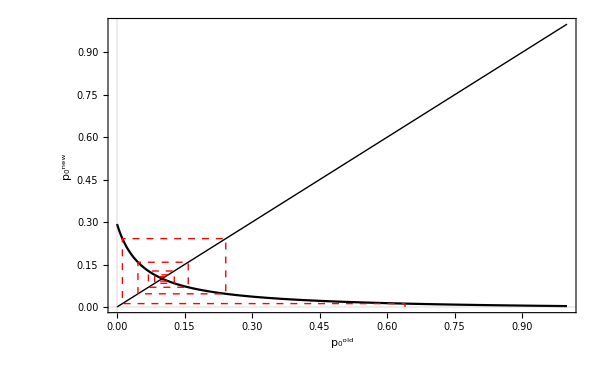

```mathematica
CobwebPlot[f(1-fracGRDSnewPars[ϕ,f,fmu,#,T])/.{ϕ->0.02,f->0.33,fmu->0.5,T->3}&,0.64,10,{0,1},PlotRange->{{0,1},{0,1}},Frame->True,Axes->False,CobStyle->Directive[Dashed,Red],PlotRangePadding->None,FrameLabel->{{"p_0^new",},{"p_0^old",""}},ImageSize->600]
```

```mathematica
Manipulate[CobwebPlot[f(1-fracGRDSnewPars[ϕ,f,fmu,#,T])/.{ϕ->0.02,f->0.33,fmu->0.5,T->3}&,p0init,10,{0,1},PlotRange->{{0,1},{0,1}},Frame->True,Axes->False,CobStyle->Directive[Dashed,Red],PlotRangePadding->None,FrameLabel->{{"p_0^new",},{"p_0^old",""}}],{{p0init,0.11},0.001,0.999}]
```

```mathematica
p0solsGRDS=Solve[(1-fracGRDSnewPars[ϕ,f,fmu,p0,T])f == p0,p0];
p0solsGRDS/.{ϕ->0.5,f-> 0.1,fmu->0.5,T-> 30}
```

{{p0→0.0234669},{p0→-0.0653312}}

Again, it is clear that we want to go with the first solution, so let’s keep that one:

```mathematica
p0solGRDS[ϕ_,f_,fmu_,T_]:=Evaluate[p0/.p0solsGRDS[[1]]]
```

### Defining the average growth rate function

We can insert this starting fraction in our function for the total number of cells (n_tot), or we can immediately calculate the average growth rate:

```mathematica
GGRDSsimplified=FullSimplify[Log[ntotGRDS[ϕ fmu,f/fmu,p0solGRDS[ϕ,f,fmu,T],T]]/T,Assumptions->{ϕ>0,f<1,f>0,fmu>0,fmu<1,T>0}];
```

```mathematica
GGRDS[ϕ_,f_,fmu_,T_]:=Evaluate[GGRDSsimplified]
GnumGRDS[ϕ_?NumericQ,f_?NumericQ,fmu_?NumericQ,T_?NumericQ]:=Evaluate[GGRDSsimplified]
```

### The optimal switching rate for both cases

We can investigate how much difference GRDS can maximally make by optimising the switching rates (ϕ) in both cases. We use an upper bound for phi of 1000 currently, because it will not really matter if this is 1000 or even larger generally.

```mathematica
optphi[f_?NumericQ,T_?NumericQ] := If[f>=fcrit[T],ϕ/.Last[FindMaximum[Evaluate[Gnum[ϕ,f,T]],{ϕ,0.1,0,MAXPHI/.GLOBALPARS}]],0]
optphiGRDS[f_?NumericQ,fmu_?NumericQ,T_?NumericQ] := ϕ/.Last[FindMaximum[Evaluate[GnumGRDS[ϕ,f,fmu,T]],{ϕ,0.1,0,MAXPHI/.GLOBALPARS}]]
```

### The limiting fraction for large T

We can again look at the limiting fraction for large T

```mathematica
largeTlimitGRDS = Limit[fracGRDSnewPars[ϕ,f,fmu,p0,t],t->Infinity,Assumptions->{ϕ>0,p0<1,p0>0,f>0,f<1,fmu<1,fmu>0}]
```

(2 f ϕ+p0 (1-f ϕ-fmu ϕ+√(f^2 ϕ^2+(-1+fmu ϕ)^2+2 f ϕ (1+fmu ϕ))))/(-1+2 p0+f ϕ+fmu ϕ+√(f^2 ϕ^2+(-1+fmu ϕ)^2+2 f ϕ (1+fmu ϕ)))

And we can check if it is still independent of p0. We use our manually obtained expression to check with Mathematica’s expression

```mathematica
p0LargeTGRDS =Simplify[1/2 (1+√D-f ϕ-ϕ fmu)/.{D-> 1+ϕ fmu (-2+ϕ fmu+f/fmu (2+(2+f/fmu) ϕ fmu))}]
FullSimplify[largeTlimitGRDS==1/2 (1+√D-f ϕ-ϕ fmu),D==1+ϕ fmu (-2+ϕ fmu+f/fmu (2+(2+f/fmu) ϕ fmu))]
```

1/2 (1-f ϕ-fmu ϕ+√(f^2 ϕ^2+(-1+fmu ϕ)^2+2 f ϕ (1+fmu ϕ)))

True

Let’s compare this with the original limiting fraction

```mathematica
p0LargeTnoGRDS = Simplify[1/2 (1+√D-f ϕ-ϕ)/.{D->1+ϕ (-2+ϕ+f (2+(2+f) ϕ))}]
```

1/2 (1-(1+f) ϕ+√(1+2 (-1+f) ϕ+(1+f)^2 ϕ^2))

```mathematica
parsGRDS={f->fslide,fmu->fmuslide,T->20,p0->0.1};
Manipulate[Plot[{1/2 (1-f ϕ-fmu ϕ+√(f^2 ϕ^2+(-1+fmu ϕ)^2+2 f ϕ (1+fmu ϕ)))/.{p0->0.1},1/2 (1-(1+f) ϕ+√(1+2 (-1+f) ϕ+(1+f)^2 ϕ^2))/.{p0->0.1}},{ϕ,0.001,3},FrameLabel->{{"Final fraction p(T)",},{"Switching rate ϕ",Style["large T limit of fraction",Bold]}},PlotLegends->{"GRDS","Original"}],{{f,0.1},0.001,0.999},{{fmu,0.1},0.001,0.999}]
```

### Limit for very fast switching

As before without GRDS, if switching is very fast, the fraction of cells in the adapted phenotype is determined solely by the difference in switching rate. This results in the following fraction of adapted cells, and thus also in this average population growth rate:

```mathematica
limFracLargePhiGRDS=Limit[fracGRDS2[ϕ,f,fmu,p0,T],ϕ->Infinity,Assumptions->{f<1,f>0,fmu<1,fmu>0,p0<1,p0>0,T>0}]
```

Limit[fracGRDS2[ϕ,f,fmu,p0,T],ϕ→∞,Assumptions→{f<1,f>0,fmu<1,fmu>0,p0<1,p0>0,T>0}]

## Analysis of difference with and without GRDS

From this point on, we will again return to the parameters as used in the paper, i.e. r_μ=1/f_μ gives the factor difference between fast and slow switching (captures the strength of GRDS), n-1=1/f give the number of non-adapted phenotypes (captures the difficulty of the adaptation problem). Different than in the main text of the paper: when we indicate a switching rate ϕ, we mean the switching rate away from non-adapted phenotypes, so ϕ=ϕ_0

### Some visual examinations of the average growth rate as function of parameters

In the slider-plot below, one can see that a high r_μ (high difference in switching rates) usually increases the growth rates. Also, we see that the optimal ϕ is usually finite when f_μ is larger than f, while the optimal ϕ becomes infinite for f_μ<f.

```mathematica
Manipulate[Plot[Evaluate[GGRDS[ϕ,1/nminus1,1/rmu,T]]/.{rmu->rmuslide,nminus1->nminus1slide,T->Tslide},{ϕ,0.01,100},Frame->True,FrameStyle->Black,PlotRange->{0,1},FrameLabel -> {"Switching rate ϕ","Average growth rate"},ImageSize -> 600,BaseStyle -> {FontFamily -> "Helvetica",FontSize -> 14}],{{rmuslide,10},1,1000},{{nminus1slide,10},1,1000},{{Tslide,10},0.01,20}]
```

It would be useful to know whether the optimal r_μ is always as high as possible. This seems indeed to be the case in realistic scenarios, although not when ϕ is too small. The reason is that switching rates are so small that the population is not bet hedging properly, decreasing the switching rates even further by GRDS is not optimal.

```mathematica
Manipulate[Plot[Evaluate[GGRDS[ϕ,1/nminus1,1/rmu,T]]/.{ϕ->phislide,nminus1->nminus1slide,T->Tslide},{rmu,1,1000},PlotRange->Full,Frame->True,FrameStyle->Black,FrameLabel -> {"Strengt of GRDS (r_μ)","Average growth rate"},ImageSize -> 600,BaseStyle -> {FontFamily -> "Helvetica",FontSize -> 14}],{{phislide,0.1},0.001,3},{{nminus1slide,10},10,1000},{{Tslide,10},0.01,20}]
```

### The effect of r_μ

What is the effect of growth rate dependent switching. In many cases, the stronger GRDS is, the better. The following expression for the derivative will not show us much. To show this, we start from the optimal switching rate for the original model, and try if it becomes any better if we add some growth rate dependence. It is clear that for all tested parameters, the growth rates increase with GRDS.

```mathematica
p1=Plot[Evaluate@Table[Log[GnumGRDS[optphi[1/nminus1,T],1/nminus1,10^-logrmu,T]/Gnum[optphi[1/nminus1,T],1/nminus1,T]]/.{T->20},{nminus1,{2,10,100,1000}}],{logrmu,-1,3},PlotLegends->LineLegend[Table[nminus1,{nminus1,{2,10,100,1000}}],LegendLabel->"n-1"],FrameLabel->{{"Log(G_GRDS/G_bet)",},{"log(r_μ)",""}},ImageSize->400,ImagePadding->{{100,20},{80,40}}];
p2=Plot[Evaluate@Table[Log[GnumGRDS[optphi[1/nminus1,T],1/nminus1,10^-logrmu,T]/Gnum[optphi[1/nminus1,T],1/nminus1,T]]/.{nminus1->10},{T,{1,2,5,10,100}}],{logrmu,-1,3},PlotLegends->LineLegend[Table[T,{T,{1,2,5,10,100}}],LegendLabel->T],FrameLabel->{{"Log(G_GRDS/G_conv)",},{"log(r_μ)",""}},ImageSize->400,ImagePadding->{{100,20},{80,40}}];
GraphicsColumn[{p1,p2},ImageSize->600,Spacings->-40]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

From this, it seems relatively clear that GRDS can give a clear initial advantage. Also, it seems that larger r_μ will always give a larger advantage. So let’s use this in the optimisation, we will set r_μ to some upper bound

### Contourplots showing average growth rate as function of the three parameters

We analyse the effect of the three parameters 1) r_μ, 2) T, 3) n-1, by making contourplots of 2-D slices of the three-dimensional parameter space.

#### Make function for getting time dynamics for given parameter set

Sometimes, we will want to highlight a certain parameter set. Here is a function that does that for us.

```mathematica
getTimeDynamics=Function[{Nminus1,rmu,T,color,imagesize},
Quiet[f=1/Nminus1;fmu=1/rmu;
optphi=optphiGRDS[f,fmu,T];
pt=Plot[fracGRDSNum[optphi ,f,fmu,p0solGRDS[optphi,f,fmu,T],t],{t,0,T},PlotStyle->{Thickness[0.02],LineColor->color},ImagePadding->{{40,10},{120,40}},PlotRange->{{0,T},{0,1}},FrameLabel->{{"Adapted fraction",},{"Time",Style[StringForm["T=``, (n-1)=``, r_μ=``",Round[T],Round[Nminus1],Round[rmu]],Bold]}},ImageSize->imagesize],{FindMaximum::lstol}];
{optphi,pt}];
```

#### Contourplots showing effects of r_μ and n-1

We define a general plotting function that makes a contourplot of the average growth rate depending on the strength of GRDS, and the complexity of the regulation problem.

```mathematica
makeMuContourPlotFmuN=Function[{T,plotpoints,imagesize},
ContourPlot[GnumGRDS[optphiGRDS[10^-logphen,10^-logfoldchange,T],10^-logphen,10^-logfoldchange,T],{logfoldchange,0,3},{logphen,0,3},ColorFunction->(ColorData["M10DefaultDensityGradient"][0+1#]&),ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},FrameLabel->{{"# of bad phenotypes: n-1",},{"Fold change switching rate: r_μ",Style[StringForm["Average growth rate if T=``",T],Bold]}},ImageSize->imagesize,ImagePadding->{{80,40},{50,60}},PlotLegends->BarLegend[{Automatic,{0,1}},{Automatic,11}],PlotRange->All,PlotPoints->plotpoints,FrameTicks->{{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None},{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None}}]];
```

And a similar function to plot the optimal switching rates ϕ:

```mathematica
makePhiContourPlotFmuN=Function[{T,plotpoints},
Quiet[ContourPlot[optphiGRDS[10^-logphen,10^-logfoldchange,T],{logfoldchange,0,3},{logphen,0,3},ScalingFunctions->"Log10" ,Contours->{-3,-2,-1,0,1,2,3},FrameLabel->{{"# of bad phenotypes: n-1",},{"Fold change switching rate: r_μ",Style[StringForm["Optimal switching rate (Cell["ϕ",ExpressionUUID->"7664ebee-f568-4907-81e9-0c160af2285a"]) if T=``",T],Bold]}},ImageSize->400,ImagePadding->{{80,40},{50,60}},PlotLegends->BarLegend[{Automatic,{.001,1000}},{Automatic,11}],PlotRange->All,PlotPoints->plotpoints,FrameTicks->{{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None},{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None}}],{FindMinimum::reged,FindMaximum::lstol,FindMaximum::nrnum}]];
```

Here follows an example:

```mathematica
pt3=makeMuContourPlotFmuN[10,20,400];
pt4=makePhiContourPlotFmuN[10,3]; (*The plotting of optimal phi is very slow, therefore we only take 3 plotpoints. Increase this for higher resolution.*)
GraphicsRow[{pt3,pt4},ImageSize->800,Spacings->0]
```

-Graphics-

#### Contourplots showing effects of r_μ and T

We define a general plotting function that makes a contourplot of the average growth rate depending on the strength of GRDS, and the average duration of the environments.

```mathematica
makeMuContourPlotFmuT=Function[{Nminus1,plotpoints,imagesize},
ContourPlot[GnumGRDS[optphiGRDS[1/Nminus1,10^-logfoldchange,10^logT],1/Nminus1,10^-logfoldchange,10^logT],{logfoldchange,0,3},{logT,0,3},ColorFunction->(ColorData["M10DefaultDensityGradient"][0+1#]&),ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},FrameLabel->{{"Environment duration: T",},{"Fold change switching rate: r_μ",Style[StringForm["Average growth rate if # bad phenotypes=``",Nminus1],Bold]}},ImageSize->imagesize,ImagePadding->{{80,40},{50,60}},PlotLegends->BarLegend[{Automatic,{0,1}},{Automatic,11}],PlotRange->All,PlotPoints->plotpoints,FrameTicks->{{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None},{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None}}]];
```

And a similar function to plot the optimal switching rates ϕ:

```mathematica
makePhiContourPlotFmuT=Function[{Nminus1,plotpoints},
Quiet[ContourPlot[optphiGRDS[1/Nminus1,10^-logfoldchange,10^T],{logfoldchange,0,3},{T,0,3},ScalingFunctions->"Log10" ,Contours->{-3,-2,-1,0,1,2,3},FrameLabel->{{"Environment duration: T",},{"Fold change switching rate: r_μ",Style[StringForm["Optimal switching rate (ϕ) if # bad phenotypes=``",Nminus1],Bold]}},ImageSize->400,ImagePadding->{{80,40},{50,60}},PlotLegends->BarLegend[{Automatic,{.001,1000}},{Automatic,11}],PlotRange->All,PlotPoints->plotpoints,FrameTicks->{{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None},{Table[{y,ToString[Round[10^y,0.001]]},{y,0,3}],None}}],{FindMinimum::reged,FindMaximum::lstol,FindMaximum::nrnum}]];
```

Here follows an example:

```mathematica
pt3=makeMuContourPlotFmuT[100,20,400];
pt4=makePhiContourPlotFmuT[100,3]; (*The plotting of optimal phi is very slow, therefore we only take 3 plotpoints. Increase this for higher resolution.*)
GraphicsRow[{pt3, pt4},ImageSize->800,Spacings->0]
```

FindMinimum::reged: The point {0.} is at the edge of the search region {0.,1000.} in coordinate 1 and the computed search direction points outside the region.

-Graphics-

Note that the optimal phi calculation seems to be wrong and very noisy. We will examine this a bit more below, but making contourplots seems to be beyond mathematica’s abilities.

### Combining contourplots with time dynamics

We define some functions that combine a contourplot showing dependence of average growth rates on parameters, with some highlighted time dynamics for specific parameter sets.

```mathematica
getContourPlusTimeDynamicsFmuNAdapted=Function[{T,plotpoints,parsSets},
contourfmuN=makeMuContourPlotFmuN[T,plotpoints,400];
pos=Table[{Log10[rmu],Log10[Nminus1]}/.parsSets[[i]],{i,1,3}];
posInfos=Table[getTimeDynamics[Nminus1/.parsSets[[i]],rmu/.parsSets[[i]],T,apple4[[i]],300],{i,1,3}];
contour=Show[contourfmuN,Epilog->{PointSize[0.05],Table[{apple4[[ii]],Point[pos[[ii]]]},{ii,1,3}],Table[Text[StringForm[" ϕ_μ = `` ",Round[posInfos[[j]][[1]]/rmu/.parsSets[[j]],0.0001]],Offset[{10,0},pos[[j]]],{Left,Center},Background->None,BaseStyle->{FontFamily->"Helvetica",Black}],{j,1,3}]}];
inset=GraphicsRow[Table[posInfos[[k]][[2]],{k,1,2}],ImageSize->400,Spacings->-80];
GraphicsColumn[{contour,inset},ImageSize->800,Spacings->-90]];
```

```mathematica
getContourPlusTimeDynamicsFmuTAdapted=Function[{NMinus1,plotpoints,parsSets},
contourfmuT=makeMuContourPlotFmuT[NMinus1,plotpoints,400];
pos=Table[{Log10[rmu],Log10[T]}/.parsSets[[i]],{i,1,3}];
posInfos=Table[getTimeDynamics[NMinus1,rmu/.parsSets[[i]],T/.parsSets[[i]],apple4[[i]],300],{i,1,3}];
contour=Show[contourfmuT,Epilog->{PointSize[0.05],Table[{apple4[[ii]],Point[pos[[ii]]]},{ii,1,3}],Table[Text[StringForm[" ϕ_μ = `` ",Round[posInfos[[j]][[1]]/rmu/.parsSets[[j]],0.0001]],Offset[{10,0},pos[[j]]],{Left,Center},Background->None,BaseStyle->{FontFamily->"Helvetica",Black}],{j,1,3}]}];
inset=GraphicsRow[Table[posInfos[[k]][[2]],{k,1,2}],ImageSize->400,Spacings->-80];
GraphicsColumn[{contour,inset},ImageSize->800,Spacings->-90]];
```

```mathematica
parsSetsTimeDynamicsfmuT={{rmu->10^2,T->10^1},{rmu->10^1,T->10^2},{rmu->10^1,T->10^1}};
parsSetsTimeDynamicsfmuN={{Nminus1->10^1,rmu->10^1},{Nminus1->10^2,rmu->10^1},{Nminus1->10^2,rmu->10^2}};
apple4={green,red,grey,purple};
contourTimeDynamicsT10combined=getContourPlusTimeDynamicsFmuNAdapted[10,20,parsSetsTimeDynamicsfmuN];Print["Done first."];
apple4={grey,purple,red,green};
contourTimeDynamicsN100combined=getContourPlusTimeDynamicsFmuTAdapted[100,20,parsSetsTimeDynamicsfmuT];
```

Done first.

FindMinimum::reged: The point {0.} is at the edge of the search region {0.,1000.} in coordinate 1 and the computed search direction points outside the region.

```mathematica
GraphicsRow[{contourTimeDynamicsT10combined,contourTimeDynamicsN100combined},ImageSize->1600,Spacings->-80]
```

-Graphics-

### Optimal switching at long environment durations

#### Plots that show optimal switching rates

To get some insight in the dependence of the optimal switching rate on the parameters, we plot G as a function of ϕ for different parameter sets.

```mathematica
plotPhiVSG=Function[{nminus1,T},
Quiet[
rmus={1,5,10,50,100};
pt1=LogLinearPlot[Evaluate@Table[GGRDS[ϕ,1/nminus1,1/rmu,T],{rmu,rmus}],{ϕ,10^-3,1000},PlotLegends->LineLegend[Table[rmu,{rmu,rmus}],LegendLabel->Style[Subscript[r, μ],FontFamily->"Helvetica", FontSize->20],LabelStyle->{FontFamily->"Helvetica",FontSize->20}],FrameLabel->{{"G",},{"ϕ_μ",StringForm["n-1 = ``, T = ``",nminus1,T]}},ImageSize->600,ImagePadding->{{80,20},{80,40}}];
optphis=Table[optphiGRDS[1/nminus1,1/rmus[[ii]],T],{ii,1,5}];,{FindMaximum::lstol,FindMaximum::nrnum,General::munfl,FindMinimum::reged}];
Show[pt1,Epilog->{PointSize[0.025],Table[{ColorData["VibrantColor"/.colormaps,ii],Point[{Log[optphis[[ii]]],GGRDS[optphis[[ii]],1/nminus1,1/rmus[[ii]],T]}]},{ii,1,5}]}]];
plotPhiVSGvaryT=Function[{nminus1,rmu},
Quiet[
Ts={1,5,10,50,100};
pt1=LogLinearPlot[Evaluate@Table[GGRDS[ϕ,1/nminus1,1/rmu,T],{T,Ts}],{ϕ,10^-3,1000},PlotLegends->LineLegend[Table[T,{T,Ts}],LegendLabel->Style[T,FontFamily->"Helvetica", FontSize->20],LabelStyle->{FontFamily->"Helvetica",FontSize->20}],FrameLabel->{{"G",},{"ϕ_μ",StringForm["n-1 = ``, r_μ = ``",nminus1,rmu]}},ImageSize->600,ImagePadding->{{80,20},{80,40}}];
optphis=Table[optphiGRDS[1/nminus1,1/rmu,Ts[[ii]]],{ii,1,5}];,{FindMaximum::lstol,FindMaximum::nrnum,General::munfl,FindMinimum::reged}];
Show[pt1,Epilog->{PointSize[0.025],Table[{ColorData["VibrantColor"/.colormaps,ii],Point[{Log[optphis[[ii]]],GGRDS[optphis[[ii]],1/nminus1,1/rmu,Ts[[ii]]]}]},{ii,1,5}]}]];
plotPhiVSGvaryN=Function[{rmu,T},
Quiet[
nminus1s={1,5,10,50,100};
pt1=LogLinearPlot[Evaluate@Table[GGRDS[ϕ,1/nminus1,1/rmu,T],{nminus1,nminus1s}],{ϕ,10^-3,1000},PlotLegends->LineLegend[Table[nminus1,{nminus1,nminus1s}],LegendLabel->Style[n-1,FontFamily->"Helvetica", FontSize->20],LabelStyle->{FontFamily->"Helvetica",FontSize->20}],FrameLabel->{{"G",},{"ϕ_μ",StringForm["r_μ = ``, T = ``",rmu,T]}},ImageSize->600,ImagePadding->{{80,20},{80,40}}];
optphis=Table[optphiGRDS[1/nminus1s[[ii]],1/rmu,T],{ii,1,5}];,{FindMaximum::lstol,FindMaximum::nrnum,General::munfl,FindMinimum::reged}];
Show[pt1,Epilog->{PointSize[0.025],Table[{ColorData["VibrantColor"/.colormaps,ii],Point[{Log[optphis[[ii]]],GGRDS[optphis[[ii]],1/nminus1s[[ii]],1/rmu,T]}]},{ii,1,5}]}]];
```

Because the figures below (on the left) indicate that the switching rate away from non-adapted phenotypes tends to follow ϕ_0=r_μ/T, we also plot G dependent on ϕ_0 r_μ/T.

```mathematica
plotPhiRmuTVSG=Function[{nminus1,T},
Quiet[
rmus={1,5,10,50,100};
pt1=Plot[Evaluate@Table[GGRDS[phiRmuT rmu/T,1/nminus1,1/rmu,T],{rmu,rmus}],{phiRmuT,10^-3,10},PlotLegends->LineLegend[Table[rmu,{rmu,rmus}],LegendLabel->Style[Subscript[r, μ],FontFamily->"Helvetica", FontSize->20],LabelStyle->{FontFamily->"Helvetica",FontSize->20}],FrameLabel->{{"G",},{"ϕ_μT",StringForm["n-1 = ``, T = ``",nminus1,T]}},ImageSize->600,ImagePadding->{{80,20},{80,40}}];
optphis=Table[optphiGRDS[1/nminus1,1/rmus[[ii]],T],{ii,1,5}];,{FindMaximum::lstol,FindMaximum::nrnum,General::munfl,FindMinimum::reged}];
Show[pt1,Epilog->{PointSize[0.025],Table[{ColorData["VibrantColor"/.colormaps,ii],Point[{optphis[[ii]]/rmus[[ii]] T,GGRDS[optphis[[ii]],1/nminus1,1/rmus[[ii]],T]}]},{ii,1,5}],{AbsoluteThickness[2],Dashing[0.01],Black,Line[{{1,0},{1,1}}]}}]];
plotPhiRmuTVSGvaryT=Function[{nminus1,rmu},
Quiet[
Ts={1,5,10,50,100};
pt1=Plot[Evaluate@Table[GGRDS[phiRmuT rmu/T,1/nminus1,1/rmu,T],{T,Ts}],{phiRmuT,10^-3,10},PlotLegends->LineLegend[Table[T,{T,Ts}],LegendLabel->Style[T,FontFamily->"Helvetica", FontSize->20],LabelStyle->{FontFamily->"Helvetica",FontSize->20}],FrameLabel->{{"G",},{"ϕ_μT",StringForm["Cell["n-1",ExpressionUUID->"e396c3ed-3efd-49ec-b10c-b315d5d37331"] = ``, r_μ = ``",nminus1,rmu]}},ImageSize->600,ImagePadding->{{80,20},{80,40}}];
optphis=Table[optphiGRDS[1/nminus1,1/rmu,Ts[[ii]]],{ii,1,5}];,{FindMaximum::lstol,FindMaximum::nrnum,General::munfl,FindMinimum::reged}];
Show[pt1,Epilog->{PointSize[0.025],Table[{ColorData["VibrantColor"/.colormaps,ii],Point[{optphis[[ii]]/rmu Ts[[ii]],GGRDS[optphis[[ii]],1/nminus1,1/rmu,Ts[[ii]]]}]},{ii,1,5}],{AbsoluteThickness[2],Dashing[0.01],Black,Line[{{1,0},{1,1}}]}}]];
plotPhiRmuTVSGvaryN=Function[{rmu,T},
Quiet[
nminus1s={5,10,50,100};
pt1=Plot[Evaluate@Table[GGRDS[phiRmuT rmu/T,1/nminus1,1/rmu,T],{nminus1,nminus1s}],{phiRmuT,10^-3,10},PlotLegends->LineLegend[Table[nminus1,{nminus1,nminus1s}],LegendLabel->Style[n-1,FontFamily->"Helvetica", FontSize->20],LabelStyle->{FontFamily->"Helvetica",FontSize->20}],FrameLabel->{{"G",},{"ϕ_μT",StringForm["r_μ = ``, T = ``",rmu,T]}},ImageSize->600,ImagePadding->{{80,20},{80,40}}];
optphis=Table[optphiGRDS[1/nminus1s[[ii]],1/rmu,T],{ii,1,4}];,{FindMaximum::lstol,FindMaximum::nrnum,General::munfl,FindMinimum::reged}];
Show[pt1,Epilog->{PointSize[0.025],Table[{ColorData["VibrantColor"/.colormaps,ii],Point[{optphis[[ii]]/rmu T,GGRDS[optphis[[ii]],1/nminus1s[[ii]],1/rmu,T]}]},{ii,1,4}],{AbsoluteThickness[2],Dashing[0.01],Black,Line[{{1,0},{1,1}}]}}]];
```

```mathematica
pars={logn->2,logT->1};
ptphiG=plotPhiVSG[10^logn/.pars,10^logT/.pars];Print["First done."];
ptphiRmuTG=plotPhiRmuTVSG[10^logn/.pars,10^logT/.pars];Print["Second done."];
pars={logn->2,logrmu->1};
ptphiGvaryT=plotPhiVSGvaryT[10^logn/.pars,10^logrmu/.pars];Print["Third done."];
ptphiRmuTGvaryT=plotPhiRmuTVSGvaryT[10^logn/.pars,10^logrmu/.pars];Print["Fourth done."];
pars={logT->1,logrmu->1};
ptphiGvaryN=plotPhiVSGvaryN[10^logrmu/.pars,10^logT/.pars];Print["First done."];
ptphiRmuTGvaryN=plotPhiRmuTVSGvaryN[10^logrmu/.pars,10^logT/.pars];Print["Sixth done."];
```

First done.

Second done.

Third done.

Fourth done.

First done.

Sixth done.

```mathematica
GraphicsGrid[{{ptphiG,ptphiRmuTG},{ptphiGvaryT,ptphiRmuTGvaryT},{ptphiGvaryN,ptphiRmuTGvaryN}},ImageSize->1500,Spacings->-40]
```

-Graphics-

#### Checking the analytical expression for the fitness benefit

In the analytical analysis of the long-time limit in this minimal model, we found that the fitness benefit of GRDS should be given by G_GRDS-G_bet=1/T log((1+r_μ)/2). We can check this numerically:

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::reged: The point {0.} is at the edge of the search region {0.,1000.} in coordinate 1 and the computed search direction points outside the region.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

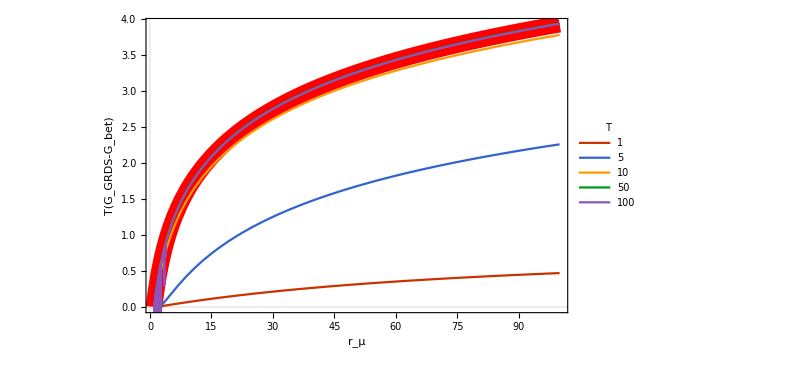

```mathematica
pars={nminus1->100};
Ts={1,5,10,50,100};
pt1=Plot[Log[(1+rmu)/2],{rmu,1,100},ImageSize->600,FrameLabel->{{"T(G_GRDS-G_bet)",},{"r_μ",StringForm["Cell["n-1",ExpressionUUID->"ddc31d87-887e-46b7-bd1d-2166dfda21bd"] = ``",100]}},PlotStyle->{Red,Thickness[0.02]}];
pt2=Plot[Evaluate@Table[T(GnumGRDS[optphiGRDS[1/nminus1,1/rmu,T],1/nminus1,1/rmu,T]-Gnum[optphi[1/nminus1,T],1/nminus1,T])/.pars,{T,Ts}],{rmu,1,100},PlotLegends->LineLegend[Table[T,{T,Ts}],LegendLabel->Style[T,FontFamily->"Helvetica", FontSize->20],LabelStyle->{FontFamily->"Helvetica",FontSize->20}],ImageSize->600,ImagePadding->{{80,20},{80,40}}];
Show[pt1,pt2]
```

### Optimal switching at short environment durations

We have already found above that for small environment durations, T, and large enough f, the optimal switching rate for bet-hedging populations is zero. Does this change when we introduce GRDS?

```mathematica
logrmus={0,0.1,0.2,0.5,1,3};
Manipulate[Plot[Evaluate@Table[GGRDS[ϕ,10^-logn,10^-logrmu,1]/.{logn->lognslide},{logrmu,logrmus}],{ϕ,0.01,100},PlotLegends->LineLegend[Table[logrmu,{logrmu,logrmus}],LegendLabel->"log10(r_μ)"],Frame->True,FrameStyle->Black,PlotRange->{0,1},FrameLabel -> {"Switching rate ϕ","Average growth rate"},ImageSize -> 600,BaseStyle -> {FontFamily -> "Helvetica",FontSize -> 14}],{{lognslide,1},0,3}]
```

We see that even a little bit of GRDS already makes it optimal to use a very large switching rate (from r_μ>10^0.5). We can see for which strength of GRDS the switch is made from small to large optimal ϕ.

FindMinimum::reged: The point {0.} is at the edge of the search region {0.,1000.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindMinimum::reged will be suppressed during this calculation.

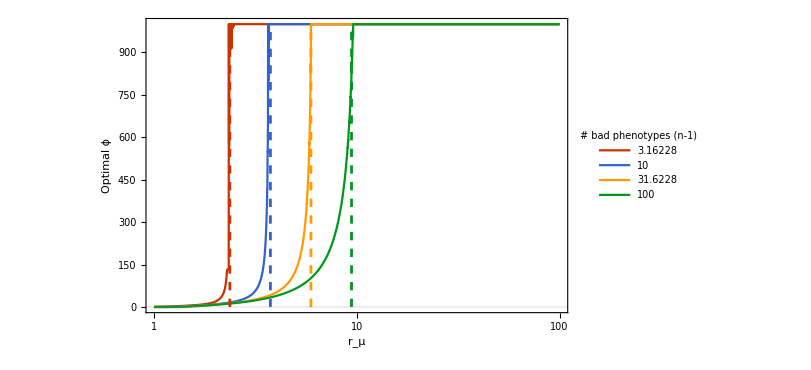

```mathematica
logns={.5,1,1.5,2};
LogLinearPlot[Evaluate@Table[optphiGRDS[10^-logn,1/rmu,1],{logn,logns}],{rmu,1,100},PlotLegends->LineLegend[Table[10^logn,{logn,logns}],LegendLabel->"# bad phenotypes (n-1)"],Frame->True,FrameStyle->Black,FrameLabel -> {"r_μ","Optimal ϕ"},ImageSize -> 600,BaseStyle -> {FontFamily -> "Helvetica",FontSize -> 14},Epilog->{AbsoluteThickness[2],Dashing[0.01],Table[{ColorData["VibrantColor"/.colormaps,ii],Line[{{Log[Exp[a](10^logns[[ii]])^b] ,0},{Log[Exp[a](10^logns[[ii]])^b],1000}}/.{a->0.4,b->0.4}]},{ii,1,4}]}]
```

It seems that the critical GRDS-strength follows approximately r_μ^crit=(e^0.4(n-1))^0.4, which probably means nothing. In any case, it is clear that for strong enough GRDS, the optimal switching rate moves from 0 to infinite. This information is used in our analytical derivation.

```mathematica
Limit[GGRDS[ϕ,f,fmu,T],ϕ->Infinity,Assumptions->{f<1,f>0,fmu<1,fmu>0,T>0}]
```

1/11